```mathematica
SetDirectory@NotebookDirectory[]
<<FixPolygons`
```

/Users/graham/Downloads/FixPolygons-v0.2

```mathematica
g2=ContourPlot[(√2 √(M U (-κ Subscript[n, 0]-Subscript[n, 1]+√(κ^2 Subscript[n, 0]^2-2 (-2+κ) Subscript[n, 0] Subscript[n, 1]+Subscript[n, 1]^2))))/ℏ//.{ℏ->1,M->1,U->1,Subscript[n, 1]->η,Subscript[n, 0]->1-η},{κ,0,1},{η,0,1},AxesLabel->{κ,η,k},PlotPoints->100,ColorFunction->ColorData["LightTerrain"],BaseStyle->14]//FixPolygons;
```

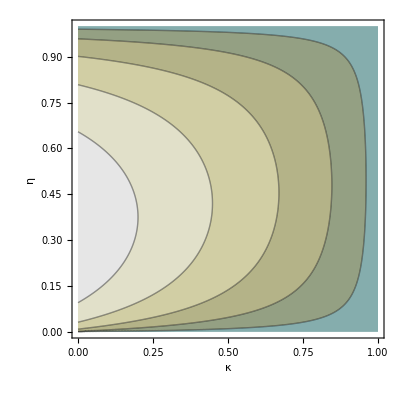

```mathematica
g2
```